# W12: Spinning Tops

Code adapted from lecture notes by P. Saeta (Harvey Mudd College).
Last revision: Nov 11, 2021, HH

## Init

```mathematica
$OutputDir="~/Documents/teach/2020_phy820/repo_devel/worksheets/w12/fig"
```

~/Documents/teach/2020_phy820/repo_devel/worksheets/w12/fig

## Euler Angles and Angular Velocities

Graphics and definitions from worksheet #10 and accompanying notebook.

### Representing the coordinate transformations

```mathematica
ShowTheAxes[ pts_, color_ ,opac_:0.2] := Graphics3D[ {color,Thick, Line[ {pts[[1]],{0,0,0},pts[[2]],{0,0,0},pts[[3]]}],
color,Opacity[opac], Polygon[{pts[[1]],pts[[2]],-pts[[1]], -pts[[2]],pts[[1]]}],
Opacity[0.6],Cone[{0.9 pts[[3]],pts[[3]]},0.05],
Sphere[pts[[1]],0.05]
 },
PlotRange->1.05,Axes->True];
ViewOpts = {AxesLabel->{x,y,z},LabelStyle->Larger,ViewPoint->{2,1,0.75}};
Show[ {ShowTheAxes[ {{1,0,0},{0,1,0},{0,0,1}}, Red]}, ViewOpts]
```

-Graphics3D-

```mathematica
d[ϕ_] := {{Cos[ϕ], Sin[ϕ], 0},{-Sin[ϕ],Cos[ϕ],0},{0,0,1}};
c[θ_] := {{1, 0, 0},{0,Cos[θ],Sin[θ]},{0,-Sin[θ],Cos[θ]}};
b[ψ_] := {{Cos[ψ], Sin[ψ], 0},{-Sin[ψ],Cos[ψ],0},{0,0,1}};
```

```mathematica
a[ϕ_,θ_,ψ_] =  b[ψ] .c[θ] .d[ϕ]; a[ϕ,θ,ψ] // MatrixForm
```

(Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ] | Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ] | Sin[θ] Sin[ψ]
-Cos[θ] Cos[ψ] Sin[ϕ]-Cos[ϕ] Sin[ψ] | Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ] | Cos[ψ] Sin[θ]
Sin[θ] Sin[ϕ] | -Cos[ϕ] Sin[θ] | Cos[θ])

```mathematica
aInv[ϕ_,θ_,ψ_] = Inverse[a[ϕ,θ,ψ]]//Simplify; aInv[ϕ,θ,ψ]//MatrixForm
```

(Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ] | -Cos[θ] Cos[ψ] Sin[ϕ]-Cos[ϕ] Sin[ψ] | Sin[θ] Sin[ϕ]
Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ] | Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ] | -Cos[ϕ] Sin[θ]
Sin[θ] Sin[ψ] | Cos[ψ] Sin[θ] | Cos[θ])

### Transformation of the basis vectors

#### Unit vectors in the body-fixed frame

```mathematica
ex = aInv[ϕ,θ,ψ] . {1,0,0}; 
ey = aInv[ϕ,θ,ψ] . {0,1,0};
ez = aInv[ϕ,θ,ψ] . {0,0,1};
```

#### Unit vectors in the space-fixed frame

```mathematica
eϕ = {0,0,1};
eθ = Transpose[d[ϕ]] . {1,0,0}; eθ//MatrixForm
eψ = Transpose[ c[θ] .d[ϕ]] . {0,0,1}; eψ//MatrixForm
```

(Cos[ϕ]
Sin[ϕ]
0)

(Sin[θ] Sin[ϕ]
-Cos[ϕ] Sin[θ]
Cos[θ])

### Angular velocity in the body-fixed frame

The total angular velocity vector in the space-fixed frame is

```mathematica
ωlab = ϕ'[t] eϕ + θ'[t] eθ + ψ'[t] eψ
```

{Cos[ϕ] θ'[t]+Sin[θ] Sin[ϕ] ψ'[t],Sin[ϕ] θ'[t]-Cos[ϕ] Sin[θ] ψ'[t],ϕ'[t]+Cos[θ] ψ'[t]}

We can project it on each of the body-fixed basis vectors to get the components in the body-fixed frame:

```mathematica
ω1 = ωlab . ex//Simplify
```

Cos[ψ] θ'[t]+Sin[θ] Sin[ψ] ϕ'[t]

```mathematica
ω2 = ωlab . ey //Simplify
```

-Sin[ψ] θ'[t]+Cos[ψ] Sin[θ] ϕ'[t]

```mathematica
ω3 = ωlab . ez //Simplify
```

Cos[θ] ϕ'[t]+ψ'[t]

## Top

```mathematica
top[ϕ_,θ_,ψ_,opa_:0.25 ] := Module[{m,center, radline},
m = b[ψ] .c[θ] . d[ϕ];
center = Flatten[{0,0,1}.m];
radline = Flatten[{1/3,0,1} . m];
Graphics3D[{Opacity[opa],EdgeForm[Opacity[opa]],Cone[  {center ,{0,0,0}}, 1/3],
Blue,Thick,Line[{ {0,0,0},radline } ],
Yellow,Thick,Line[{ {0,0,0}, Flatten[{-1/3,0,1}.m] }]} ]
]
```

```mathematica
top[0,0,0]
```

-Graphics3D-

```mathematica
Manipulate[Show[ {
ShowTheAxes[ IdentityMatrix[3], Blue,0],
ShowTheAxes[ d[ϕ], Red,0.1], 
ShowTheAxes[ c[θ] .d[ϕ], Green],
ShowTheAxes[b[ψ] . c[θ] . d[ϕ], Black, 0.3 ],top[ϕ,θ,ψ, 0.5]
}, ViewOpts],
{ϕ,0,2π},{θ,0,π},{ψ,0,2π}]
```

Show::gcomb: Could not combine the graphics objects in ….

## Symmetric Heavy Top

### Solution for the top dropped (spinning) from rest

Double - checking the math :

```mathematica
ClearAll[L,A,CC]
```

```mathematica
L=1/2 A(θ'[t]^2+ϕ'[t]^2Sin[θ[t]]^2)+1/2CC(ψ'[t]+ϕ'[t]Cos[θ[t]])^2-M g l Cos[θ[t]]
```

-g l M Cos[θ[t]]+1/2 A (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)+1/2 CC (Cos[θ[t]] ϕ'[t]+ψ'[t])^2

The equations of motion are:

```mathematica
eqθ=D[D[L,θ'[t]],t] ==D[L,θ[t]]//Simplify
```

A θ''[t]==Sin[θ[t]] (g l M+(A-CC) Cos[θ[t]] ϕ'[t]^2-CC ϕ'[t] ψ'[t])

```mathematica
eqϕ=D[L,ϕ'[t]]==pϕ
```

A Sin[θ[t]]^2 ϕ'[t]+CC Cos[θ[t]] (Cos[θ[t]] ϕ'[t]+ψ'[t])==pϕ

```mathematica
eqψ=D[L,ψ'[t]]==pψ
```

CC (Cos[θ[t]] ϕ'[t]+ψ'[t])==pψ

```mathematica
sol=Solve[{eqψ,eqϕ},{ϕ'[t],ψ'[t]}]//Simplify
```

{{ϕ'[t]→((pϕ-pψ Cos[θ[t]]) Csc[θ[t]]^2)/A,ψ'[t]→(A pψ+CC pψ Cot[θ[t]]^2-CC pϕ Cot[θ[t]] Csc[θ[t]])/(A CC)}}

```mathematica
eqθ//.sol//Simplify
```

{A θ''[t]==1/A(pψ^2 Cot[θ[t]]^3-pϕ pψ Csc[θ[t]]-2 pϕ pψ Cot[θ[t]]^2 Csc[θ[t]]+Cot[θ[t]] (pψ^2+pϕ^2 Csc[θ[t]]^2)+A g l M Sin[θ[t]])}

### Equations of Motion

As a concrete example, assume that C=A/2=1/2 and that β =Mgl = 1.

```mathematica
CC = 1/2; A = 1; β = 1;
```

Integration of energy conservation behaved iffy, so let' s try equations of motion directly.

```mathematica
topSol[ θ0_ ,pϕ_,pψ_] := NDSolve[ {
θ''[t] == -(pϕ-pψ Cos[θ[t]])(pψ- pϕ Cos[θ[t]])/(A^2 Sin[θ[t]]^3) + β /A  Sin[θ[t]],
ϕ'[t] ==  (pϕ -pψ Cos[θ[t]])/(A  Sin[θ[t]]^2),
 ψ'[t] ==pψ/CC-(pϕ -pψ Cos[θ[t]] ) Cos[θ[t]]/(A  Sin[θ[t]]^2),
ϕ[0] == 0, ψ[0] == 0,
θ'[0] == 0,
θ[0] == θ0},{θ, ϕ, ψ},{t,0,50},MaxSteps->10^5]
```

#### Category I

Categories refer to worksheet #12, figs 3a-c.

```mathematica
ts = topSol[Pi/6,2,2.1]
```

{{θ→InterpolatingFunction[{{0., 50.}}, <>],ϕ→InterpolatingFunction[{{0., 50.}}, <>],ψ→InterpolatingFunction[{{0., 50.}}, <>]}}

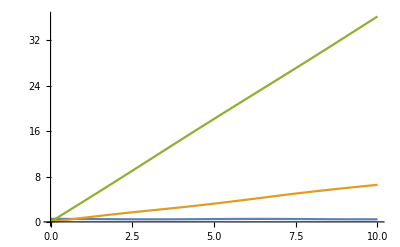

```mathematica
Plot[Evaluate[{θ[t],ϕ[t],ψ[t]} /. ts ],{t,0,10}]
```

```mathematica
Animate[Show[ Evaluate[ {
ShowTheAxes[ IdentityMatrix[3], Blue,0],
ShowTheAxes[b[ ψ[t] ] .c[ θ[t]] . d[ ϕ[t] ], Black, 0.3 ],
top[ϕ[t], θ[t], ψ[t], 0.5]
} /. ts], 
 AxesLabel->{"x","y","z"},ViewPoint->{2,1,0.75}],
{t,0,50},AnimationRate->0.3,AnimationRunning->False]
```

```mathematica
Show[{Graphics3D[ {Opacity->0.5,Sphere[{0,0,0},1]}],
ParametricPlot3D[ Evaluate[
{Sin[θ[t]] Cos[ϕ[t]],Sin[θ[t]] Sin[ϕ[t]],Cos[θ[t]]} /. ts],
{t,0,50}, PlotRange->{-1.1,1.1},PlotStyle->Thick]
 }]
```

-Graphics3D-

#### Category II

```mathematica
ts = topSol[Pi/6,2,2.4]
```

{{θ→InterpolatingFunction[{{0., 50.}}, <>],ϕ→InterpolatingFunction[{{0., 50.}}, <>],ψ→InterpolatingFunction[{{0., 50.}}, <>]}}

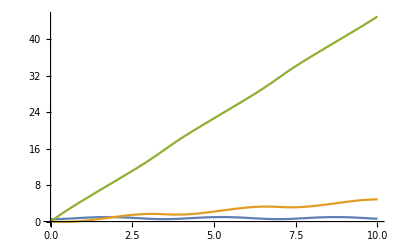

```mathematica
Plot[Evaluate[{θ[t],ϕ[t],ψ[t]} /. ts ],{t,0,10}]
```

```mathematica
Animate[Show[ Evaluate[ {
ShowTheAxes[ IdentityMatrix[3], Blue,0],
ShowTheAxes[b[ ψ[t] ] .c[ θ[t]] . d[ ϕ[t] ], Black, 0.3 ],
top[ϕ[t], θ[t], ψ[t], 0.5]
} /. ts], 
 AxesLabel->{"x","y","z"},ViewPoint->{2,1,0.75}],
{t,0,50},AnimationRate->0.3,AnimationRunning->False]
```

```mathematica
Show[{Graphics3D[ {Opacity->0.5,Sphere[{0,0,0},1]}],
ParametricPlot3D[ Evaluate[
{Sin[θ[t]] Cos[ϕ[t]],Sin[θ[t]] Sin[ϕ[t]],Cos[θ[t]]} /. ts],
{t,0,50}, PlotRange->{-1.1,1.1},PlotStyle->Thick]
 }]
```

-Graphics3D-

#### Category III

Categories refer to worksheet #12, figs 3a-c.

```mathematica
ts = topSol[Pi/6,2,2.3]
```

{{θ→InterpolatingFunction[{{0., 50.}}, <>],ϕ→InterpolatingFunction[{{0., 50.}}, <>],ψ→InterpolatingFunction[{{0., 50.}}, <>]}}

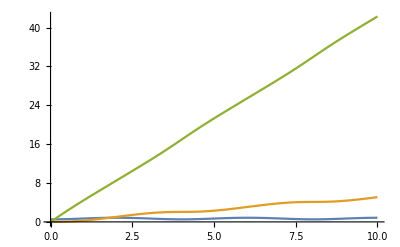

```mathematica
Plot[Evaluate[{θ[t],ϕ[t],ψ[t]} /. ts ],{t,0,10}]
```

```mathematica
Animate[Show[ Evaluate[ {
ShowTheAxes[ IdentityMatrix[3], Blue,0],
ShowTheAxes[b[ ψ[t] ] .c[ θ[t]] . d[ ϕ[t] ], Black, 0.3 ],
top[ϕ[t], θ[t], ψ[t], 0.5]
} /. ts], 
 AxesLabel->{"x","y","z"},ViewPoint->{2,1,0.75}],
{t,0,50},AnimationRate->0.3,AnimationRunning->False]
```

```mathematica
Show[{Graphics3D[ {Opacity->0.5,Sphere[{0,0,0},1]}],
ParametricPlot3D[ Evaluate[
{Sin[θ[t]] Cos[ϕ[t]],Sin[θ[t]] Sin[ϕ[t]],Cos[θ[t]]} /. ts],
{t,0,50}, PlotRange->{-1.1,1.1},PlotStyle->Thick]
 }]
```

-Graphics3D-